# Quantica

## Calculator of quantum systems with mathematica

20 December, 2013

## Energy domain problem

いくつかの固有値問題を解いてみましょう．

### 調和振動子

次のハミルトニアンで定義される調和振動子のエネルギー及び，固有状態を求める．

H(q,p) = p^2/2 +q^2/2

もちろんエネルギーは

E = ℏ(n+1/2)   (n=0, 1, 2⋯)

である．

```mathematica
Needs["Quantica`"];
Quantica`MP`dps=20;
T[x_]:=x^2/2
V[x_]:=x^2/2
dim=40;
domain={{-2,2},{-2,2}};
QuanticaSetting[dim,domain,Verbose->True];
SetSystem[T,V];
Ham=Quantica`FourierBase`Hamiltonian[];

{evals,evecs}=Eigen[Ham];
Print[Re[evals][[1;;5]]/Hbar]
```

{Dim:,40,Domain:,{{-2,2},{-2,2}},Tau:,1,dps:,20}

{0.5,1.5,2.5,3.5,4.5}

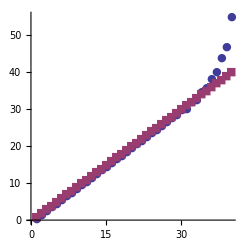

```mathematica
ListPlot[{Table[{i,Re[evals[[i]]/Hbar ] },{i,1,dim}],
Table[{i,i},{i,1,dim}]},
PlotMarkers->{Automatic,Small},ImageSize->{245,245},AspectRatio->Full]
```

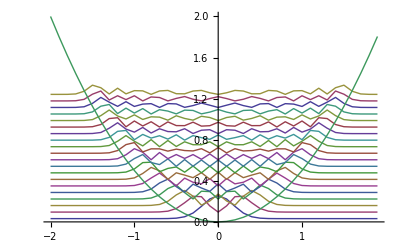

```mathematica
potential=Table[{X[[1]][[i]],V[X[[1]]][[i]]},{i,1,dim}];
data[n_] := Table[ { X[[1]][[i]],Quantica`State`Abs2[ evecs[[n]][[i]]] + evals[[n]]},{i,1,dim}];
datalist=Append[Map[data,Range[dim/2]],potential];
ListPlot[ datalist,
Joined->True,PlotRange->All]
```

#### 用いた関数の定義

```mathematica
?Quantica`MP`dps
?QuanticaSetting
?SetSystem
?Quantica`FourierBase`Hamiltonian
?Eigen
```

the decimal precision (defalt 20)

QuanticaSetting[dim, domain, tau=1 ],

dim: real integer

domain: 2x2 list such as {{qmin,qmax}, {pmin,pmax}}. 各変数の精度は∞でなければならない
,
tau:(optional) 精度は∞でなければならない

SetSystem[T,V]: Kinetic function and Potential function

return Hamilton matrix <q'|H(q,p)|q>

{evalues,evectors}=Eigen[mat,sort:True]
 return eigenvalue and eigenvectors

### Kicked rotator

ハミルトニアン

H(q,p,t) = T(p) + V(q)∑_(n∈ℤ) δ(t-n)

で定義される時間発展演算子(量子写像Qmapと呼ぶ事にする)

U(t+1,t)=exp[-i/ℏT(p)]exp[-i/ℏV(p)]

の固有値問題を考える．いまTおよびVの定義は

T(p)=p^2/2,    V(q)=k/(4 π^2)Cos(2πq)

を考える.

```mathematica
Needs["Quantica`"];
Quantica`MP`dps=20;
k=1;
T[x_]:=x^2/2
V[x_]:=k*Cos[2*Pi*x]/(4*Pi*Pi)
dim=40;
domain={{0,1},{0,1}};
QuanticaSetting[dim,domain, Verbose->True];
SetSystem[T,V];
mat = Quantica`Qmap`Unitary[];
{evals,evecs}=Eigen[mat];
```

{Dim:,40,Domain:,{{0,1},{0,1}},Tau:,1,dps:,20}

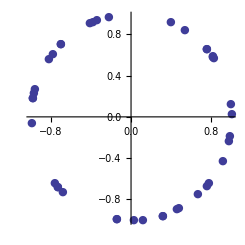

```mathematica
ListPlot[Table[{Re[evals[[i]]],Im[evals[[i]]]},{i,1,Length[evals]}],PlotMarkers->{Automatic,Small},ImageSize->{245,245},AspectRatio->Full]
```

#### 用いた関数の定義

```mathematica
?Quantica`MP`dps
?QuanticaSetting
?SetSystem
?Quantica`Qmap`Unitary
?Eigen
```

the decimal precision (defalt 20)

QuanticaSetting[dim, domain, tau=1 ],

dim: integer >1 and even number,

domain: 2x2 list such as {{qmin,qmax}, {pmin,pmax}}. each variables request a ratoinal value
,
tau:(optional) rational value

SetSystem[T,V]: Kinetic function and Potential function

return unitary matrix <q'|U|q>

{evalues,evectors}=Eigen[mat,sort:True]
 return eigenvalue and eigenvectors

## Related Links

Notes on Scientific Computing with Python